Underdamped 2

```mathematica
$Assumptions={τ>0,γ>0,ω0>0,√(-γ^2+4 ω0^2)>0,τR Re[s]>-1,τ>=t>=0};
```

```mathematica
Psi[t_]=ⅇ^(-γ Abs[t]) ((2 ω0^2)/(-γ^2+4 ω0^2)+((-γ^2+2 ω0^2) Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)+(γ Sin[√(-γ^2+4 ω0^2) Abs[t]])/(√(-γ^2+4 ω0^2)));
dPsi[t_]=-(2 ⅇ^(-γ Abs[t]) γ ω0^2 Sign[t])/(-γ^2+4 ω0^2)+ⅇ^(-γ Abs[t]) γ Cos[t √(-γ^2+4 ω0^2)] Sign[t]+(ⅇ^(-γ Abs[t]) γ^3 Cos[t √(-γ^2+4 ω0^2)] Sign[t])/(-γ^2+4 ω0^2)-(2 ⅇ^(-γ Abs[t]) γ ω0^2 Cos[t √(-γ^2+4 ω0^2)] Sign[t])/(-γ^2+4 ω0^2)-(2 ⅇ^(-γ Abs[t]) ω0^2 Sin[t √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2));
ddPsi1[t_]=-2 ⅇ^(-γ Abs[t]) ω0^2 Cos[t √(-γ^2+4 ω0^2)]+(2 ⅇ^(-γ Abs[t]) γ^2 ω0^2)/(-γ^2+4 ω0^2)-ⅇ^(-γ Abs[t]) γ^2 Cos[t √(-γ^2+4 ω0^2)] -(ⅇ^(-γ Abs[t]) γ^4 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)+(2 ⅇ^(-γ Abs[t]) γ^2 ω0^2 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)-(ⅇ^(-γ Abs[t]) γ^3 Sign[t] Sin[t √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2))+(4 ⅇ^(-γ Abs[t]) γ ω0^2 Sign[t] Sin[t √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2))-ⅇ^(-γ Abs[t]) γ √(-γ^2+4 ω0^2) Sign[t] Sin[t √(-γ^2+4 ω0^2)];
ddPsi2[t_]=-(4 ⅇ^(-γ Abs[t]) γ ω0^2)/(-γ^2+4 ω0^2)+2 ⅇ^(-γ Abs[t]) γ Cos[t √(-γ^2+4 ω0^2)]+(2 ⅇ^(-γ Abs[t]) γ^3 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)-(4 ⅇ^(-γ Abs[t]) γ ω0^2 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2);
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi1[t]+ddPsi2[t]DiracDelta[t],t,s]);

c0=SeriesCoefficient[f[s],{s,0,0}]

c1=SeriesCoefficient[f[s],{s,0,1}]

c2=SeriesCoefficient[f[s],{s,0,2}]
```

-1/(4 γ^2)+1/(2 ω0^2)

1/(8 γ^3)

-1/(16 γ^4)

```mathematica
τR=(γ^2+ω0^2)/(2 γ ω0^2);

g[t_]=(t+τR)/(τ+2τR);

h1[t_]=t/τ;
h2[t_]=t/τ+Sin[π t/τ];
```

```mathematica
Wh1[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi1[t-u]h1[t]h1[u],{t,0,τ},{u,0,τ}]-ddPsi2[0]/2 Integrate[h1[t]^2,{t,0,τ}]
```

```mathematica
Wh2[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi1[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ}]-ddPsi2[0]/2 Integrate[h2[t]^2,{t,0,τ}]
```

-1/2 (5/6+2/π) τ (2 γ+(2 γ^3)/(-γ^2+4 ω0^2)-(8 γ ω0^2)/(-γ^2+4 ω0^2))+1/2 ((2 ω0^2)/(-γ^2+4 ω0^2)+(-γ^2+2 ω0^2)/(-γ^2+4 ω0^2))-1/((-γ^2+4 ω0^2) (γ^2+ω0^2+γ τ ω0^2))ⅇ^(-γ τ) ω0^2 (-γ^2-ⅇ^(γ τ) γ^3 τ+ω0^2+4 ⅇ^(γ τ) γ τ ω0^2+γ^2 Cos[τ √(-γ^2+4 ω0^2)]-ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-γ √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)])-(4 ⅇ^(-γ τ) (ⅇ^(γ τ) π^12 γ^6+10 ⅇ^(γ τ) π^10 γ^8 τ^2+33 ⅇ^(γ τ) π^8 γ^10 τ^4+40 ⅇ^(γ τ) π^6 γ^12 τ^6+16 ⅇ^(γ τ) π^4 γ^14 τ^8-4 ⅇ^(γ τ) π^12 γ^4 ω0^2-56 ⅇ^(γ τ) π^10 γ^6 τ^2 ω0^2-228 ⅇ^(γ τ) π^8 γ^8 τ^4 ω0^2-304 ⅇ^(γ τ) π^6 γ^10 τ^6 ω0^2-128 ⅇ^(γ τ) π^4 γ^12 τ^8 ω0^2+2 ⅇ^(γ τ) π^12 γ^2 ω0^4+84 ⅇ^(γ τ) π^10 γ^4 τ^2 ω0^4-2 ⅇ^(γ τ) π^12 γ^4 τ^2 ω0^4+546 ⅇ^(γ τ) π^8 γ^6 τ^4 ω0^4-20 ⅇ^(γ τ) π^10 γ^6 τ^4 ω0^4+976 ⅇ^(γ τ) π^6 γ^8 τ^6 ω0^4-66 ⅇ^(γ τ) π^8 γ^8 τ^6 ω0^4+640 ⅇ^(γ τ) π^4 γ^10 τ^8 ω0^4-80 ⅇ^(γ τ) π^6 γ^10 τ^8 ω0^4+128 ⅇ^(γ τ) π^2 γ^12 τ^10 ω0^4-32 ⅇ^(γ τ) π^4 γ^12 τ^10 ω0^4+8 π^12 ω0^6-8 ⅇ^(γ τ) π^12 ω0^6+8 π^12 γ τ ω0^6+80 π^10 γ^2 τ^2 ω0^6-112 ⅇ^(γ τ) π^10 γ^2 τ^2 ω0^6+8 ⅇ^(γ τ) π^12 γ^2 τ^2 ω0^6+80 π^10 γ^3 τ^3 ω0^6+8 π^11 γ^3 τ^3 ω0^6+264 π^8 γ^4 τ^4 ω0^6-840 ⅇ^(γ τ) π^8 γ^4 τ^4 ω0^6-8 π^10 γ^4 τ^4 ω0^6+104 ⅇ^(γ τ) π^10 γ^4 τ^4 ω0^6+264 π^8 γ^5 τ^5 ω0^6+72 π^9 γ^5 τ^5 ω0^6-8 ⅇ^(γ τ) π^9 γ^5 τ^5 ω0^6-4 ⅇ^(γ τ) π^10 γ^5 τ^5 ω0^6+320 π^6 γ^6 τ^6 ω0^6-2144 ⅇ^(γ τ) π^6 γ^6 τ^6 ω0^6-64 π^8 γ^6 τ^6 ω0^6+392 ⅇ^(γ τ) π^8 γ^6 τ^6 ω0^6+320 π^6 γ^7 τ^7 ω0^6+192 π^7 γ^7 τ^7 ω0^6-72 ⅇ^(γ τ) π^7 γ^7 τ^7 ω0^6-36 ⅇ^(γ τ) π^8 γ^7 τ^7 ω0^6+128 π^4 γ^8 τ^8 ω0^6-2176 ⅇ^(γ τ) π^4 γ^8 τ^8 ω0^6-128 π^6 γ^8 τ^8 ω0^6+480 ⅇ^(γ τ) π^6 γ^8 τ^8 ω0^6+128 π^4 γ^9 τ^9 ω0^6+128 π^5 γ^9 τ^9 ω0^6-192 ⅇ^(γ τ) π^5 γ^9 τ^9 ω0^6-96 ⅇ^(γ τ) π^6 γ^9 τ^9 ω0^6-768 ⅇ^(γ τ) π^2 γ^10 τ^10 ω0^6+256 ⅇ^(γ τ) π^4 γ^10 τ^10 ω0^6-128 ⅇ^(γ τ) π^3 γ^11 τ^11 ω0^6-64 ⅇ^(γ τ) π^4 γ^11 τ^11 ω0^6-128 π^10 τ^2 ω0^8+128 ⅇ^(γ τ) π^10 τ^2 ω0^8-128 π^10 γ τ^3 ω0^8-768 π^8 γ^2 τ^4 ω0^8+960 ⅇ^(γ τ) π^8 γ^2 τ^4 ω0^8-96 ⅇ^(γ τ) π^10 γ^2 τ^4 ω0^8-768 π^8 γ^3 τ^5 ω0^8-128 π^9 γ^3 τ^5 ω0^8+32 ⅇ^(γ τ) π^9 γ^3 τ^5 ω0^8+16 ⅇ^(γ τ) π^10 γ^3 τ^5 ω0^8-1152 π^6 γ^4 τ^6 ω0^8+2816 ⅇ^(γ τ) π^6 γ^4 τ^6 ω0^8+128 π^8 γ^4 τ^6 ω0^8-640 ⅇ^(γ τ) π^8 γ^4 τ^6 ω0^8-1152 π^6 γ^5 τ^7 ω0^8-640 π^7 γ^5 τ^7 ω0^8+320 ⅇ^(γ τ) π^7 γ^5 τ^7 ω0^8+160 ⅇ^(γ τ) π^8 γ^5 τ^7 ω0^8-512 π^4 γ^6 τ^8 ω0^8+3520 ⅇ^(γ τ) π^4 γ^6 τ^8 ω0^8+512 π^6 γ^6 τ^8 ω0^8-736 ⅇ^(γ τ) π^6 γ^6 τ^8 ω0^8-512 π^4 γ^7 τ^9 ω0^8-512 π^5 γ^7 τ^9 ω0^8+928 ⅇ^(γ τ) π^5 γ^7 τ^9 ω0^8+464 ⅇ^(γ τ) π^6 γ^7 τ^9 ω0^8+1792 ⅇ^(γ τ) π^2 γ^8 τ^10 ω0^8-576 ⅇ^(γ τ) π^4 γ^8 τ^10 ω0^8+640 ⅇ^(γ τ) π^3 γ^9 τ^11 ω0^8+320 ⅇ^(γ τ) π^4 γ^9 τ^11 ω0^8+256 ⅇ^(γ τ) γ^10 τ^12 ω0^8+768 π^8 τ^4 ω0^10-768 ⅇ^(γ τ) π^8 τ^4 ω0^10+768 π^8 γ τ^5 ω0^10+2560 π^6 γ^2 τ^6 ω0^10-3072 ⅇ^(γ τ) π^6 γ^2 τ^6 ω0^10+512 ⅇ^(γ τ) π^8 γ^2 τ^6 ω0^10+2560 π^6 γ^3 τ^7 ω0^10+768 π^7 γ^3 τ^7 ω0^10-128 ⅇ^(γ τ) π^7 γ^3 τ^7 ω0^10-64 ⅇ^(γ τ) π^8 γ^3 τ^7 ω0^10+2816 π^4 γ^4 τ^8 ω0^10-4864 ⅇ^(γ τ) π^4 γ^4 τ^8 ω0^10-768 π^6 γ^4 τ^8 ω0^10+768 ⅇ^(γ τ) π^6 γ^4 τ^8 ω0^10+2816 π^4 γ^5 τ^9 ω0^10+1792 π^5 γ^5 τ^9 ω0^10-512 ⅇ^(γ τ) π^5 γ^5 τ^9 ω0^10-256 ⅇ^(γ τ) π^6 γ^5 τ^9 ω0^10+1024 π^2 γ^6 τ^10 ω0^10-3584 ⅇ^(γ τ) π^2 γ^6 τ^10 ω0^10-1024 π^4 γ^6 τ^10 ω0^10+512 ⅇ^(γ τ) π^4 γ^6 τ^10 ω0^10+1024 π^2 γ^7 τ^11 ω0^10+1024 π^3 γ^7 τ^11 ω0^10-896 ⅇ^(γ τ) π^3 γ^7 τ^11 ω0^10-448 ⅇ^(γ τ) π^4 γ^7 τ^11 ω0^10-1024 ⅇ^(γ τ) γ^8 τ^12 ω0^10+512 ⅇ^(γ τ) π^2 γ^8 τ^12 ω0^10-512 ⅇ^(γ τ) π γ^9 τ^13 ω0^10-256 ⅇ^(γ τ) π^2 γ^9 τ^13 ω0^10-2048 π^6 τ^6 ω0^12+2048 ⅇ^(γ τ) π^6 τ^6 ω0^12-2048 π^6 γ τ^7 ω0^12-4096 π^4 γ^2 τ^8 ω0^12+4608 ⅇ^(γ τ) π^4 γ^2 τ^8 ω0^12-1536 ⅇ^(γ τ) π^6 γ^2 τ^8 ω0^12-4096 π^4 γ^3 τ^9 ω0^12-2048 π^5 γ^3 τ^9 ω0^12-512 ⅇ^(γ τ) π^5 γ^3 τ^9 ω0^12-256 ⅇ^(γ τ) π^6 γ^3 τ^9 ω0^12-2048 π^2 γ^4 τ^10 ω0^12+3072 ⅇ^(γ τ) π^2 γ^4 τ^10 ω0^12+2048 π^4 γ^4 τ^10 ω0^12-1536 ⅇ^(γ τ) π^4 γ^4 τ^10 ω0^12-2048 π^2 γ^5 τ^11 ω0^12-2048 π^3 γ^5 τ^11 ω0^12+1024 ⅇ^(γ τ) π^3 γ^5 τ^11 ω0^12+512 ⅇ^(γ τ) π^4 γ^5 τ^11 ω0^12+512 ⅇ^(γ τ) γ^6 τ^12 ω0^12-2560 ⅇ^(γ τ) π^2 γ^6 τ^12 ω0^12+1536 ⅇ^(γ τ) π γ^7 τ^13 ω0^12+768 ⅇ^(γ τ) π^2 γ^7 τ^13 ω0^12-512 ⅇ^(γ τ) γ^8 τ^14 ω0^12+2048 π^4 τ^8 ω0^14-2048 ⅇ^(γ τ) π^4 τ^8 ω0^14+2048 π^4 γ τ^9 ω0^14+4096 π^2 γ^2 τ^10 ω0^14-4096 ⅇ^(γ τ) π^2 γ^2 τ^10 ω0^14+2048 ⅇ^(γ τ) π^4 γ^2 τ^10 ω0^14+4096 π^2 γ^3 τ^11 ω0^14+2048 π^3 γ^3 τ^11 ω0^14+2048 ⅇ^(γ τ) π^3 γ^3 τ^11 ω0^14+1024 ⅇ^(γ τ) π^4 γ^3 τ^11 ω0^14+2048 γ^4 τ^12 ω0^14-2048 ⅇ^(γ τ) γ^4 τ^12 ω0^14-2048 π^2 γ^4 τ^12 ω0^14+2048 ⅇ^(γ τ) π^2 γ^4 τ^12 ω0^14+2048 γ^5 τ^13 ω0^14+2048 π γ^5 τ^13 ω0^14+2048 ⅇ^(γ τ) π γ^5 τ^13 ω0^14+1024 ⅇ^(γ τ) π^2 γ^5 τ^13 ω0^14+2048 ⅇ^(γ τ) γ^6 τ^14 ω0^14-π^12 γ^6 Cos[τ √(-γ^2+4 ω0^2)]-10 π^10 γ^8 τ^2 Cos[τ √(-γ^2+4 ω0^2)]-33 π^8 γ^10 τ^4 Cos[τ √(-γ^2+4 ω0^2)]-40 π^6 γ^12 τ^6 Cos[τ √(-γ^2+4 ω0^2)]-16 π^4 γ^14 τ^8 Cos[τ √(-γ^2+4 ω0^2)]+4 π^12 γ^4 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^5 τ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+56 π^10 γ^6 τ^2 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-20 π^10 γ^7 τ^3 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+228 π^8 γ^8 τ^4 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-66 π^8 γ^9 τ^5 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+304 π^6 γ^10 τ^6 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-80 π^6 γ^11 τ^7 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+128 π^4 γ^12 τ^8 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-32 π^4 γ^13 τ^9 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^2 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+6 π^12 γ^3 τ ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-84 π^10 γ^4 τ^2 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+92 π^10 γ^5 τ^3 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-546 π^8 γ^6 τ^4 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+390 π^8 γ^7 τ^5 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-976 π^6 γ^8 τ^6 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+528 π^6 γ^9 τ^7 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-640 π^4 γ^10 τ^8 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+224 π^4 γ^11 τ^9 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-128 π^2 γ^12 τ^10 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^2 τ^2 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-96 π^10 γ^3 τ^3 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-8 π^11 γ^3 τ^3 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+576 π^8 γ^4 τ^4 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-768 π^8 γ^5 τ^5 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-80 π^9 γ^5 τ^5 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+1824 π^6 γ^6 τ^6 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-1504 π^6 γ^7 τ^7 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-264 π^7 γ^7 τ^7 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+2048 π^4 γ^8 τ^8 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-1088 π^4 γ^9 τ^9 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-320 π^5 γ^9 τ^9 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+768 π^2 γ^10 τ^10 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-256 π^2 γ^11 τ^11 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-128 π^3 γ^11 τ^11 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-192 π^8 γ^2 τ^4 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^2 τ^4 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+576 π^8 γ^3 τ^5 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+160 π^9 γ^3 τ^5 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-1664 π^6 γ^4 τ^6 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+192 π^8 γ^4 τ^6 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+2432 π^6 γ^5 τ^7 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+960 π^7 γ^5 τ^7 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-3008 π^4 γ^6 τ^8 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+544 π^6 γ^6 τ^8 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+3136 π^4 γ^7 τ^9 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+1440 π^5 γ^7 τ^9 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-1792 π^2 γ^8 τ^10 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+640 π^4 γ^8 τ^10 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+1280 π^2 γ^9 τ^11 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+640 π^3 γ^9 τ^11 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-256 γ^10 τ^12 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+256 π^2 γ^10 τ^12 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^2 τ^6 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-256 π^8 γ^2 τ^6 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1536 π^6 γ^3 τ^7 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-896 π^7 γ^3 τ^7 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]+2048 π^4 γ^4 τ^8 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1536 π^6 γ^4 τ^8 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-3584 π^4 γ^5 τ^9 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-2304 π^5 γ^5 τ^9 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]+2560 π^2 γ^6 τ^10 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-2304 π^4 γ^6 τ^10 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-2560 π^2 γ^7 τ^11 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1920 π^3 γ^7 τ^11 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]+1024 γ^8 τ^12 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^8 τ^12 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-512 γ^9 τ^13 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-512 π γ^9 τ^13 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-512 π^4 γ^2 τ^8 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^2 τ^8 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 π^4 γ^3 τ^9 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 π^5 γ^3 τ^9 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^4 τ^10 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1024 π^4 γ^4 τ^10 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+3072 π^2 γ^5 τ^11 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+3072 π^3 γ^5 τ^11 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]-512 γ^6 τ^12 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+512 π^2 γ^6 τ^12 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 γ^7 τ^13 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 π γ^7 τ^13 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+π^12 γ^5 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+10 π^10 γ^7 τ^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+33 π^8 γ^9 τ^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+40 π^6 γ^11 τ^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+16 π^4 γ^13 τ^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^3 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+2 π^12 γ^4 τ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-36 π^10 γ^5 τ^2 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+20 π^10 γ^6 τ^3 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-162 π^8 γ^7 τ^4 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+66 π^8 γ^8 τ^5 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-224 π^6 γ^9 τ^6 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+80 π^6 γ^10 τ^7 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-96 π^4 γ^11 τ^8 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+32 π^4 γ^12 τ^9 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^2 τ ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^3 τ^2 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-52 π^10 γ^4 τ^3 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+288 π^8 γ^5 τ^4 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-258 π^8 γ^6 τ^5 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+608 π^6 γ^7 τ^6 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-368 π^6 γ^8 τ^7 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+480 π^4 γ^9 τ^8 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-160 π^4 γ^10 τ^9 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+128 π^2 γ^11 τ^10 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^2 τ^3 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+8 π^11 γ^2 τ^3 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-192 π^8 γ^3 τ^4 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+384 π^8 γ^4 τ^5 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+80 π^9 γ^4 τ^5 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-896 π^6 γ^5 τ^6 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+928 π^6 γ^6 τ^7 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+264 π^7 γ^6 τ^7 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1216 π^4 γ^7 τ^8 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+832 π^4 γ^8 τ^9 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+320 π^5 γ^8 τ^9 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^2 γ^9 τ^10 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+256 π^2 γ^10 τ^11 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+128 π^3 γ^10 τ^11 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-192 π^8 γ^2 τ^5 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-96 π^9 γ^2 τ^5 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^3 τ^6 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-128 π^8 γ^3 τ^6 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1152 π^6 γ^4 τ^7 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-576 π^7 γ^4 τ^7 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1280 π^4 γ^5 τ^8 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^6 γ^5 τ^8 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1728 π^4 γ^6 τ^9 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-864 π^5 γ^6 τ^9 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1024 π^2 γ^7 τ^10 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-640 π^4 γ^7 τ^10 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-768 π^2 γ^8 τ^11 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-384 π^3 γ^8 τ^11 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+256 γ^9 τ^12 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-256 π^2 γ^9 τ^12 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^2 τ^7 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+384 π^7 γ^2 τ^7 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^4 γ^3 τ^8 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^3 τ^8 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1536 π^4 γ^4 τ^9 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1280 π^5 γ^4 τ^9 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^5 τ^10 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1024 π^4 γ^5 τ^10 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1536 π^2 γ^6 τ^11 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1408 π^3 γ^6 τ^11 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 γ^7 τ^12 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^2 γ^7 τ^12 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 γ^8 τ^13 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π γ^8 τ^13 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^4 γ^2 τ^9 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^5 γ^2 τ^9 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^4 τ^11 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1024 π^3 γ^4 τ^11 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 γ^6 τ^13 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π γ^6 τ^13 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]))/(γ^2 τ^2 (-ⅈ π+γ τ)^2 (ⅈ π+γ τ)^2 (γ^2-4 ω0^2) (π^4+4 π^2 γ^2 τ^2-8 π^2 τ^2 ω0^2+16 τ^4 ω0^4) (γ-ⅈ √(-γ^2+4 ω0^2))^2 (γ+ⅈ √(-γ^2+4 ω0^2))^2 (-ⅈ π+γ τ-ⅈ τ √(-γ^2+4 ω0^2)) (ⅈ π+γ τ-ⅈ τ √(-γ^2+4 ω0^2)) (-ⅈ π+γ τ+ⅈ τ √(-γ^2+4 ω0^2)) (ⅈ π+γ τ+ⅈ τ √(-γ^2+4 ω0^2)))

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi1[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]-ddPsi2[0]/2 Integrate[g[t]^2,{t,0,τ}];
```

```mathematica
W1[τ_]=W0[τ]+c0 dPsi[τ]/(τ+2τR)-c0/(τ+2τR)Integrate[ddPsi1[t]g[t],{t,0,τ}]+c0/(τ+2τR)Integrate[ddPsi1[τ-t]g[t],{t,0,τ}]-c0^2/(τ+2τR)^2 ddPsi1[0]+c0^2/(τ+2τR)^2 ddPsi1[τ]+c0/(τ+2τR)ddPsi2[τ];
```

```mathematica
Wh1[τ_]=-1/6 τ (2 γ+(2 γ^3)/(-γ^2+4 ω0^2)-(8 γ ω0^2)/(-γ^2+4 ω0^2))+1/2 ((2 ω0^2)/(-γ^2+4 ω0^2)+(-γ^2+2 ω0^2)/(-γ^2+4 ω0^2))-1/((-γ^2+4 ω0^2) (γ^2+ω0^2+γ τ ω0^2))ⅇ^(-γ τ) ω0^2 (-γ^2-ⅇ^(γ τ) γ^3 τ+ω0^2+4 ⅇ^(γ τ) γ τ ω0^2+γ^2 Cos[τ √(-γ^2+4 ω0^2)]-ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-γ √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)])-1/(4 γ^2 τ^2 ω0^4 (γ^2-4 ω0^2))ⅇ^(-γ τ) (ⅇ^(γ τ) γ^6-4 ⅇ^(γ τ) γ^4 ω0^2+2 ⅇ^(γ τ) γ^2 ω0^4-2 ⅇ^(γ τ) γ^4 τ^2 ω0^4+8 ω0^6-8 ⅇ^(γ τ) ω0^6+8 γ τ ω0^6+8 ⅇ^(γ τ) γ^2 τ^2 ω0^6-γ^6 Cos[τ √(-γ^2+4 ω0^2)]+4 γ^4 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 γ^5 τ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 γ^2 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+6 γ^3 τ ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+γ^5 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-2 γ^3 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+2 γ^4 τ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-2 γ^2 τ ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]);
```

```mathematica
Wh2[τ_]=-1/2 (5/6+2/π) τ (2 γ+(2 γ^3)/(-γ^2+4 ω0^2)-(8 γ ω0^2)/(-γ^2+4 ω0^2))+1/2 ((2 ω0^2)/(-γ^2+4 ω0^2)+(-γ^2+2 ω0^2)/(-γ^2+4 ω0^2))-1/((-γ^2+4 ω0^2) (γ^2+ω0^2+γ τ ω0^2))ⅇ^(-γ τ) ω0^2 (-γ^2-ⅇ^(γ τ) γ^3 τ+ω0^2+4 ⅇ^(γ τ) γ τ ω0^2+γ^2 Cos[τ √(-γ^2+4 ω0^2)]-ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-γ √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)])-(4 ⅇ^(-γ τ) (ⅇ^(γ τ) π^12 γ^6+10 ⅇ^(γ τ) π^10 γ^8 τ^2+33 ⅇ^(γ τ) π^8 γ^10 τ^4+40 ⅇ^(γ τ) π^6 γ^12 τ^6+16 ⅇ^(γ τ) π^4 γ^14 τ^8-4 ⅇ^(γ τ) π^12 γ^4 ω0^2-56 ⅇ^(γ τ) π^10 γ^6 τ^2 ω0^2-228 ⅇ^(γ τ) π^8 γ^8 τ^4 ω0^2-304 ⅇ^(γ τ) π^6 γ^10 τ^6 ω0^2-128 ⅇ^(γ τ) π^4 γ^12 τ^8 ω0^2+2 ⅇ^(γ τ) π^12 γ^2 ω0^4+84 ⅇ^(γ τ) π^10 γ^4 τ^2 ω0^4-2 ⅇ^(γ τ) π^12 γ^4 τ^2 ω0^4+546 ⅇ^(γ τ) π^8 γ^6 τ^4 ω0^4-20 ⅇ^(γ τ) π^10 γ^6 τ^4 ω0^4+976 ⅇ^(γ τ) π^6 γ^8 τ^6 ω0^4-66 ⅇ^(γ τ) π^8 γ^8 τ^6 ω0^4+640 ⅇ^(γ τ) π^4 γ^10 τ^8 ω0^4-80 ⅇ^(γ τ) π^6 γ^10 τ^8 ω0^4+128 ⅇ^(γ τ) π^2 γ^12 τ^10 ω0^4-32 ⅇ^(γ τ) π^4 γ^12 τ^10 ω0^4+8 π^12 ω0^6-8 ⅇ^(γ τ) π^12 ω0^6+8 π^12 γ τ ω0^6+80 π^10 γ^2 τ^2 ω0^6-112 ⅇ^(γ τ) π^10 γ^2 τ^2 ω0^6+8 ⅇ^(γ τ) π^12 γ^2 τ^2 ω0^6+80 π^10 γ^3 τ^3 ω0^6+8 π^11 γ^3 τ^3 ω0^6+264 π^8 γ^4 τ^4 ω0^6-840 ⅇ^(γ τ) π^8 γ^4 τ^4 ω0^6-8 π^10 γ^4 τ^4 ω0^6+104 ⅇ^(γ τ) π^10 γ^4 τ^4 ω0^6+264 π^8 γ^5 τ^5 ω0^6+72 π^9 γ^5 τ^5 ω0^6-8 ⅇ^(γ τ) π^9 γ^5 τ^5 ω0^6-4 ⅇ^(γ τ) π^10 γ^5 τ^5 ω0^6+320 π^6 γ^6 τ^6 ω0^6-2144 ⅇ^(γ τ) π^6 γ^6 τ^6 ω0^6-64 π^8 γ^6 τ^6 ω0^6+392 ⅇ^(γ τ) π^8 γ^6 τ^6 ω0^6+320 π^6 γ^7 τ^7 ω0^6+192 π^7 γ^7 τ^7 ω0^6-72 ⅇ^(γ τ) π^7 γ^7 τ^7 ω0^6-36 ⅇ^(γ τ) π^8 γ^7 τ^7 ω0^6+128 π^4 γ^8 τ^8 ω0^6-2176 ⅇ^(γ τ) π^4 γ^8 τ^8 ω0^6-128 π^6 γ^8 τ^8 ω0^6+480 ⅇ^(γ τ) π^6 γ^8 τ^8 ω0^6+128 π^4 γ^9 τ^9 ω0^6+128 π^5 γ^9 τ^9 ω0^6-192 ⅇ^(γ τ) π^5 γ^9 τ^9 ω0^6-96 ⅇ^(γ τ) π^6 γ^9 τ^9 ω0^6-768 ⅇ^(γ τ) π^2 γ^10 τ^10 ω0^6+256 ⅇ^(γ τ) π^4 γ^10 τ^10 ω0^6-128 ⅇ^(γ τ) π^3 γ^11 τ^11 ω0^6-64 ⅇ^(γ τ) π^4 γ^11 τ^11 ω0^6-128 π^10 τ^2 ω0^8+128 ⅇ^(γ τ) π^10 τ^2 ω0^8-128 π^10 γ τ^3 ω0^8-768 π^8 γ^2 τ^4 ω0^8+960 ⅇ^(γ τ) π^8 γ^2 τ^4 ω0^8-96 ⅇ^(γ τ) π^10 γ^2 τ^4 ω0^8-768 π^8 γ^3 τ^5 ω0^8-128 π^9 γ^3 τ^5 ω0^8+32 ⅇ^(γ τ) π^9 γ^3 τ^5 ω0^8+16 ⅇ^(γ τ) π^10 γ^3 τ^5 ω0^8-1152 π^6 γ^4 τ^6 ω0^8+2816 ⅇ^(γ τ) π^6 γ^4 τ^6 ω0^8+128 π^8 γ^4 τ^6 ω0^8-640 ⅇ^(γ τ) π^8 γ^4 τ^6 ω0^8-1152 π^6 γ^5 τ^7 ω0^8-640 π^7 γ^5 τ^7 ω0^8+320 ⅇ^(γ τ) π^7 γ^5 τ^7 ω0^8+160 ⅇ^(γ τ) π^8 γ^5 τ^7 ω0^8-512 π^4 γ^6 τ^8 ω0^8+3520 ⅇ^(γ τ) π^4 γ^6 τ^8 ω0^8+512 π^6 γ^6 τ^8 ω0^8-736 ⅇ^(γ τ) π^6 γ^6 τ^8 ω0^8-512 π^4 γ^7 τ^9 ω0^8-512 π^5 γ^7 τ^9 ω0^8+928 ⅇ^(γ τ) π^5 γ^7 τ^9 ω0^8+464 ⅇ^(γ τ) π^6 γ^7 τ^9 ω0^8+1792 ⅇ^(γ τ) π^2 γ^8 τ^10 ω0^8-576 ⅇ^(γ τ) π^4 γ^8 τ^10 ω0^8+640 ⅇ^(γ τ) π^3 γ^9 τ^11 ω0^8+320 ⅇ^(γ τ) π^4 γ^9 τ^11 ω0^8+256 ⅇ^(γ τ) γ^10 τ^12 ω0^8+768 π^8 τ^4 ω0^10-768 ⅇ^(γ τ) π^8 τ^4 ω0^10+768 π^8 γ τ^5 ω0^10+2560 π^6 γ^2 τ^6 ω0^10-3072 ⅇ^(γ τ) π^6 γ^2 τ^6 ω0^10+512 ⅇ^(γ τ) π^8 γ^2 τ^6 ω0^10+2560 π^6 γ^3 τ^7 ω0^10+768 π^7 γ^3 τ^7 ω0^10-128 ⅇ^(γ τ) π^7 γ^3 τ^7 ω0^10-64 ⅇ^(γ τ) π^8 γ^3 τ^7 ω0^10+2816 π^4 γ^4 τ^8 ω0^10-4864 ⅇ^(γ τ) π^4 γ^4 τ^8 ω0^10-768 π^6 γ^4 τ^8 ω0^10+768 ⅇ^(γ τ) π^6 γ^4 τ^8 ω0^10+2816 π^4 γ^5 τ^9 ω0^10+1792 π^5 γ^5 τ^9 ω0^10-512 ⅇ^(γ τ) π^5 γ^5 τ^9 ω0^10-256 ⅇ^(γ τ) π^6 γ^5 τ^9 ω0^10+1024 π^2 γ^6 τ^10 ω0^10-3584 ⅇ^(γ τ) π^2 γ^6 τ^10 ω0^10-1024 π^4 γ^6 τ^10 ω0^10+512 ⅇ^(γ τ) π^4 γ^6 τ^10 ω0^10+1024 π^2 γ^7 τ^11 ω0^10+1024 π^3 γ^7 τ^11 ω0^10-896 ⅇ^(γ τ) π^3 γ^7 τ^11 ω0^10-448 ⅇ^(γ τ) π^4 γ^7 τ^11 ω0^10-1024 ⅇ^(γ τ) γ^8 τ^12 ω0^10+512 ⅇ^(γ τ) π^2 γ^8 τ^12 ω0^10-512 ⅇ^(γ τ) π γ^9 τ^13 ω0^10-256 ⅇ^(γ τ) π^2 γ^9 τ^13 ω0^10-2048 π^6 τ^6 ω0^12+2048 ⅇ^(γ τ) π^6 τ^6 ω0^12-2048 π^6 γ τ^7 ω0^12-4096 π^4 γ^2 τ^8 ω0^12+4608 ⅇ^(γ τ) π^4 γ^2 τ^8 ω0^12-1536 ⅇ^(γ τ) π^6 γ^2 τ^8 ω0^12-4096 π^4 γ^3 τ^9 ω0^12-2048 π^5 γ^3 τ^9 ω0^12-512 ⅇ^(γ τ) π^5 γ^3 τ^9 ω0^12-256 ⅇ^(γ τ) π^6 γ^3 τ^9 ω0^12-2048 π^2 γ^4 τ^10 ω0^12+3072 ⅇ^(γ τ) π^2 γ^4 τ^10 ω0^12+2048 π^4 γ^4 τ^10 ω0^12-1536 ⅇ^(γ τ) π^4 γ^4 τ^10 ω0^12-2048 π^2 γ^5 τ^11 ω0^12-2048 π^3 γ^5 τ^11 ω0^12+1024 ⅇ^(γ τ) π^3 γ^5 τ^11 ω0^12+512 ⅇ^(γ τ) π^4 γ^5 τ^11 ω0^12+512 ⅇ^(γ τ) γ^6 τ^12 ω0^12-2560 ⅇ^(γ τ) π^2 γ^6 τ^12 ω0^12+1536 ⅇ^(γ τ) π γ^7 τ^13 ω0^12+768 ⅇ^(γ τ) π^2 γ^7 τ^13 ω0^12-512 ⅇ^(γ τ) γ^8 τ^14 ω0^12+2048 π^4 τ^8 ω0^14-2048 ⅇ^(γ τ) π^4 τ^8 ω0^14+2048 π^4 γ τ^9 ω0^14+4096 π^2 γ^2 τ^10 ω0^14-4096 ⅇ^(γ τ) π^2 γ^2 τ^10 ω0^14+2048 ⅇ^(γ τ) π^4 γ^2 τ^10 ω0^14+4096 π^2 γ^3 τ^11 ω0^14+2048 π^3 γ^3 τ^11 ω0^14+2048 ⅇ^(γ τ) π^3 γ^3 τ^11 ω0^14+1024 ⅇ^(γ τ) π^4 γ^3 τ^11 ω0^14+2048 γ^4 τ^12 ω0^14-2048 ⅇ^(γ τ) γ^4 τ^12 ω0^14-2048 π^2 γ^4 τ^12 ω0^14+2048 ⅇ^(γ τ) π^2 γ^4 τ^12 ω0^14+2048 γ^5 τ^13 ω0^14+2048 π γ^5 τ^13 ω0^14+2048 ⅇ^(γ τ) π γ^5 τ^13 ω0^14+1024 ⅇ^(γ τ) π^2 γ^5 τ^13 ω0^14+2048 ⅇ^(γ τ) γ^6 τ^14 ω0^14-π^12 γ^6 Cos[τ √(-γ^2+4 ω0^2)]-10 π^10 γ^8 τ^2 Cos[τ √(-γ^2+4 ω0^2)]-33 π^8 γ^10 τ^4 Cos[τ √(-γ^2+4 ω0^2)]-40 π^6 γ^12 τ^6 Cos[τ √(-γ^2+4 ω0^2)]-16 π^4 γ^14 τ^8 Cos[τ √(-γ^2+4 ω0^2)]+4 π^12 γ^4 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^5 τ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+56 π^10 γ^6 τ^2 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-20 π^10 γ^7 τ^3 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+228 π^8 γ^8 τ^4 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-66 π^8 γ^9 τ^5 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+304 π^6 γ^10 τ^6 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-80 π^6 γ^11 τ^7 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+128 π^4 γ^12 τ^8 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-32 π^4 γ^13 τ^9 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^2 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+6 π^12 γ^3 τ ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-84 π^10 γ^4 τ^2 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+92 π^10 γ^5 τ^3 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-546 π^8 γ^6 τ^4 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+390 π^8 γ^7 τ^5 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-976 π^6 γ^8 τ^6 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+528 π^6 γ^9 τ^7 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-640 π^4 γ^10 τ^8 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+224 π^4 γ^11 τ^9 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-128 π^2 γ^12 τ^10 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^2 τ^2 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-96 π^10 γ^3 τ^3 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-8 π^11 γ^3 τ^3 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+576 π^8 γ^4 τ^4 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-768 π^8 γ^5 τ^5 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-80 π^9 γ^5 τ^5 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+1824 π^6 γ^6 τ^6 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-1504 π^6 γ^7 τ^7 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-264 π^7 γ^7 τ^7 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+2048 π^4 γ^8 τ^8 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-1088 π^4 γ^9 τ^9 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-320 π^5 γ^9 τ^9 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]+768 π^2 γ^10 τ^10 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-256 π^2 γ^11 τ^11 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-128 π^3 γ^11 τ^11 ω0^6 Cos[τ √(-γ^2+4 ω0^2)]-192 π^8 γ^2 τ^4 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^2 τ^4 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+576 π^8 γ^3 τ^5 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+160 π^9 γ^3 τ^5 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-1664 π^6 γ^4 τ^6 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+192 π^8 γ^4 τ^6 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+2432 π^6 γ^5 τ^7 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+960 π^7 γ^5 τ^7 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-3008 π^4 γ^6 τ^8 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+544 π^6 γ^6 τ^8 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+3136 π^4 γ^7 τ^9 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+1440 π^5 γ^7 τ^9 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-1792 π^2 γ^8 τ^10 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+640 π^4 γ^8 τ^10 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+1280 π^2 γ^9 τ^11 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+640 π^3 γ^9 τ^11 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]-256 γ^10 τ^12 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+256 π^2 γ^10 τ^12 ω0^8 Cos[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^2 τ^6 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-256 π^8 γ^2 τ^6 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1536 π^6 γ^3 τ^7 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-896 π^7 γ^3 τ^7 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]+2048 π^4 γ^4 τ^8 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1536 π^6 γ^4 τ^8 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-3584 π^4 γ^5 τ^9 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-2304 π^5 γ^5 τ^9 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]+2560 π^2 γ^6 τ^10 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-2304 π^4 γ^6 τ^10 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-2560 π^2 γ^7 τ^11 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1920 π^3 γ^7 τ^11 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]+1024 γ^8 τ^12 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^8 τ^12 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-512 γ^9 τ^13 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-512 π γ^9 τ^13 ω0^10 Cos[τ √(-γ^2+4 ω0^2)]-512 π^4 γ^2 τ^8 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^2 τ^8 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 π^4 γ^3 τ^9 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 π^5 γ^3 τ^9 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^4 τ^10 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1024 π^4 γ^4 τ^10 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+3072 π^2 γ^5 τ^11 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+3072 π^3 γ^5 τ^11 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]-512 γ^6 τ^12 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+512 π^2 γ^6 τ^12 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 γ^7 τ^13 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+1536 π γ^7 τ^13 ω0^12 Cos[τ √(-γ^2+4 ω0^2)]+π^12 γ^5 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+10 π^10 γ^7 τ^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+33 π^8 γ^9 τ^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+40 π^6 γ^11 τ^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+16 π^4 γ^13 τ^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^3 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+2 π^12 γ^4 τ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-36 π^10 γ^5 τ^2 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+20 π^10 γ^6 τ^3 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-162 π^8 γ^7 τ^4 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+66 π^8 γ^8 τ^5 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-224 π^6 γ^9 τ^6 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+80 π^6 γ^10 τ^7 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-96 π^4 γ^11 τ^8 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+32 π^4 γ^12 τ^9 ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-2 π^12 γ^2 τ ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^3 τ^2 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-52 π^10 γ^4 τ^3 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+288 π^8 γ^5 τ^4 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-258 π^8 γ^6 τ^5 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+608 π^6 γ^7 τ^6 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-368 π^6 γ^8 τ^7 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+480 π^4 γ^9 τ^8 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-160 π^4 γ^10 τ^9 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+128 π^2 γ^11 τ^10 ω0^4 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+32 π^10 γ^2 τ^3 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+8 π^11 γ^2 τ^3 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-192 π^8 γ^3 τ^4 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+384 π^8 γ^4 τ^5 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+80 π^9 γ^4 τ^5 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-896 π^6 γ^5 τ^6 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+928 π^6 γ^6 τ^7 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+264 π^7 γ^6 τ^7 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1216 π^4 γ^7 τ^8 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+832 π^4 γ^8 τ^9 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+320 π^5 γ^8 τ^9 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^2 γ^9 τ^10 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+256 π^2 γ^10 τ^11 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+128 π^3 γ^10 τ^11 ω0^6 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-192 π^8 γ^2 τ^5 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-96 π^9 γ^2 τ^5 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^3 τ^6 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-128 π^8 γ^3 τ^6 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1152 π^6 γ^4 τ^7 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-576 π^7 γ^4 τ^7 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1280 π^4 γ^5 τ^8 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^6 γ^5 τ^8 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1728 π^4 γ^6 τ^9 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-864 π^5 γ^6 τ^9 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1024 π^2 γ^7 τ^10 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-640 π^4 γ^7 τ^10 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-768 π^2 γ^8 τ^11 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-384 π^3 γ^8 τ^11 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+256 γ^9 τ^12 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-256 π^2 γ^9 τ^12 ω0^8 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^2 τ^7 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+384 π^7 γ^2 τ^7 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^4 γ^3 τ^8 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^6 γ^3 τ^8 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1536 π^4 γ^4 τ^9 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1280 π^5 γ^4 τ^9 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^5 τ^10 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1024 π^4 γ^5 τ^10 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1536 π^2 γ^6 τ^11 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+1408 π^3 γ^6 τ^11 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 γ^7 τ^12 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π^2 γ^7 τ^12 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 γ^8 τ^13 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+512 π γ^8 τ^13 ω0^10 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^4 γ^2 τ^9 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π^5 γ^2 τ^9 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1024 π^2 γ^4 τ^11 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-1024 π^3 γ^4 τ^11 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 γ^6 τ^13 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-512 π γ^6 τ^13 ω0^12 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]))/(γ^2 τ^2 (-ⅈ π+γ τ)^2 (ⅈ π+γ τ)^2 (γ^2-4 ω0^2) (π^4+4 π^2 γ^2 τ^2-8 π^2 τ^2 ω0^2+16 τ^4 ω0^4) (γ-ⅈ √(-γ^2+4 ω0^2))^2 (γ+ⅈ √(-γ^2+4 ω0^2))^2 (-ⅈ π+γ τ-ⅈ τ √(-γ^2+4 ω0^2)) (ⅈ π+γ τ-ⅈ τ √(-γ^2+4 ω0^2)) (-ⅈ π+γ τ+ⅈ τ √(-γ^2+4 ω0^2)) (ⅈ π+γ τ+ⅈ τ √(-γ^2+4 ω0^2)));
```

```mathematica
W0[τ_]=-(τ (3 γ^4+6 γ^2 (1+γ τ) ω0^2+(3+2 γ τ (3+2 γ τ)) ω0^4) (2 γ+(2 γ^3)/(-γ^2+4 ω0^2)-(8 γ ω0^2)/(-γ^2+4 ω0^2)))/(24 (γ^2+ω0^2+γ τ ω0^2)^2)+1/2 ((2 ω0^2)/(-γ^2+4 ω0^2)+(-γ^2+2 ω0^2)/(-γ^2+4 ω0^2))-1/((-γ^2+4 ω0^2) (γ^2+ω0^2+γ τ ω0^2))ⅇ^(-γ τ) ω0^2 (-γ^2-ⅇ^(γ τ) γ^3 τ+ω0^2+4 ⅇ^(γ τ) γ τ ω0^2+γ^2 Cos[τ √(-γ^2+4 ω0^2)]-ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-γ √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)])-(ⅇ^(-γ τ) ω0^2 (-2 γ^4-2 ⅇ^(γ τ) γ^4-2 ⅇ^(γ τ) γ^5 τ-4 γ^2 ω0^2+9 ⅇ^(γ τ) γ^2 ω0^2-4 γ^3 τ ω0^2+6 ⅇ^(γ τ) γ^3 τ ω0^2-2 ⅇ^(γ τ) γ^4 τ^2 ω0^2+6 ω0^4-4 ⅇ^(γ τ) ω0^4+4 γ τ ω0^4+8 ⅇ^(γ τ) γ τ ω0^4+8 ⅇ^(γ τ) γ^2 τ^2 ω0^4+4 γ^4 Cos[τ √(-γ^2+4 ω0^2)]-5 γ^2 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+4 γ^3 τ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-4 γ τ ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-4 γ^3 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-γ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-4 γ^2 τ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]))/(4 (γ^2-4 ω0^2) (γ^2+ω0^2+γ τ ω0^2)^2);
```

```mathematica
W1[τ_]=-(τ (3 γ^4+6 γ^2 (1+γ τ) ω0^2+(3+2 γ τ (3+2 γ τ)) ω0^4) (2 γ+(2 γ^3)/(-γ^2+4 ω0^2)-(8 γ ω0^2)/(-γ^2+4 ω0^2)))/(24 (γ^2+ω0^2+γ τ ω0^2)^2)-((-1/(4 γ^2)+1/(2 ω0^2))^2 (-γ^2-2 ω0^2-γ^4/(-γ^2+4 ω0^2)+(4 γ^2 ω0^2)/(-γ^2+4 ω0^2)))/((τ+(γ^2+ω0^2)/(γ ω0^2))^2)+1/2 ((2 ω0^2)/(-γ^2+4 ω0^2)+(-γ^2+2 ω0^2)/(-γ^2+4 ω0^2))+((-1/(4 γ^2)+1/(2 ω0^2)) (-(4 ⅇ^(-γ Abs[τ]) γ ω0^2)/(-γ^2+4 ω0^2)+2 ⅇ^(-γ Abs[τ]) γ Cos[τ √(-γ^2+4 ω0^2)]+(2 ⅇ^(-γ Abs[τ]) γ^3 Cos[τ √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)-(4 ⅇ^(-γ Abs[τ]) γ ω0^2 Cos[τ √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)))/(τ+(γ^2+ω0^2)/(γ ω0^2))+1/(τ+(γ^2+ω0^2)/(γ ω0^2))(-1/(4 γ^2)+1/(2 ω0^2)) (-(2 ⅇ^(-γ Abs[τ]) γ ω0^2 Sign[τ])/(-γ^2+4 ω0^2)+ⅇ^(-γ Abs[τ]) γ Cos[τ √(-γ^2+4 ω0^2)] Sign[τ]+(ⅇ^(-γ Abs[τ]) γ^3 Cos[τ √(-γ^2+4 ω0^2)] Sign[τ])/(-γ^2+4 ω0^2)-(2 ⅇ^(-γ Abs[τ]) γ ω0^2 Cos[τ √(-γ^2+4 ω0^2)] Sign[τ])/(-γ^2+4 ω0^2)-(2 ⅇ^(-γ Abs[τ]) ω0^2 Sin[τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2)))-1/((-γ^2+4 ω0^2) (γ^2+ω0^2+γ τ ω0^2))ⅇ^(-γ τ) ω0^2 (-γ^2-ⅇ^(γ τ) γ^3 τ+ω0^2+4 ⅇ^(γ τ) γ τ ω0^2+γ^2 Cos[τ √(-γ^2+4 ω0^2)]-ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-γ √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)])-(ⅇ^(-γ τ) (-1/(4 γ^2)+1/(2 ω0^2)) ω0^2 (-γ^3+ⅇ^(γ τ) γ^3+γ ω0^2-4 ⅇ^(γ τ) γ ω0^2+3 γ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]))/((γ^2-4 ω0^2) (γ^2+ω0^2+γ τ ω0^2) (τ+(γ^2+ω0^2)/(γ ω0^2)))-(ⅇ^(-γ τ) (-1/(4 γ^2)+1/(2 ω0^2)) ω0^2 (γ^3+ⅇ^(γ τ) γ^3+3 γ ω0^2-4 ⅇ^(γ τ) γ ω0^2+2 γ^2 τ ω0^2-2 γ^3 Cos[τ √(-γ^2+4 ω0^2)]+γ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 γ^2 τ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+2 γ^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]+2 γ τ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]))/((γ^2-4 ω0^2) (γ^2+ω0^2+γ τ ω0^2) (τ+(γ^2+ω0^2)/(γ ω0^2)))-(ⅇ^(-γ τ) ω0^2 (-2 γ^4-2 ⅇ^(γ τ) γ^4-2 ⅇ^(γ τ) γ^5 τ-4 γ^2 ω0^2+9 ⅇ^(γ τ) γ^2 ω0^2-4 γ^3 τ ω0^2+6 ⅇ^(γ τ) γ^3 τ ω0^2-2 ⅇ^(γ τ) γ^4 τ^2 ω0^2+6 ω0^4-4 ⅇ^(γ τ) ω0^4+4 γ τ ω0^4+8 ⅇ^(γ τ) γ τ ω0^4+8 ⅇ^(γ τ) γ^2 τ^2 ω0^4+4 γ^4 Cos[τ √(-γ^2+4 ω0^2)]-5 γ^2 ω0^2 Cos[τ √(-γ^2+4 ω0^2)]+4 γ^3 τ ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-2 ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-4 γ τ ω0^4 Cos[τ √(-γ^2+4 ω0^2)]-4 γ^3 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-γ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]-4 γ^2 τ ω0^2 √(-γ^2+4 ω0^2) Sin[τ √(-γ^2+4 ω0^2)]))/(4 (γ^2-4 ω0^2) (γ^2+ω0^2+γ τ ω0^2)^2)+1/((τ+(γ^2+ω0^2)/(γ ω0^2))^2)(-1/(4 γ^2)+1/(2 ω0^2))^2 ((2 ⅇ^(-γ Abs[τ]) γ^2 ω0^2)/(-γ^2+4 ω0^2)-ⅇ^(-γ Abs[τ]) γ^2 Cos[τ √(-γ^2+4 ω0^2)]-2 ⅇ^(-γ Abs[τ]) ω0^2 Cos[τ √(-γ^2+4 ω0^2)]-(ⅇ^(-γ Abs[τ]) γ^4 Cos[τ √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)+(2 ⅇ^(-γ Abs[τ]) γ^2 ω0^2 Cos[τ √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)-(ⅇ^(-γ Abs[τ]) γ^3 Sign[τ] Sin[τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2))+(4 ⅇ^(-γ Abs[τ]) γ ω0^2 Sign[τ] Sin[τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2))-ⅇ^(-γ Abs[τ]) γ √(-γ^2+4 ω0^2) Sign[τ] Sin[τ √(-γ^2+4 ω0^2)]);
```

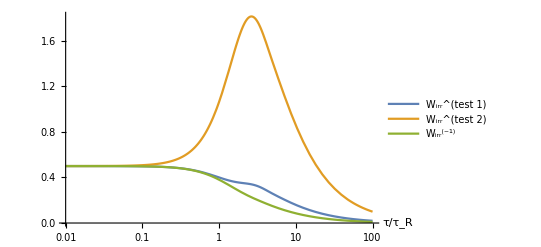

```mathematica
γ=1;
ω0=1;
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[W0[τ],"W_irr^(-1)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[γ,ω0]
```

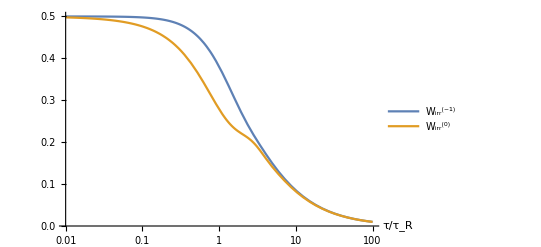

```mathematica
γ=1;
ω0=1;
LogLinearPlot[{Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[γ,ω0]
```

```mathematica
γ=1;
ω0=1;

data0=List[]


Do[

aux=Table[{τ,W0[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data0=AppendTo[data0,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi3.dat",data];

Clear[γ,ω0]
```

```mathematica
γ=1;
ω0=1;

data1=List[]


Do[

aux=Table[{τ,W0[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data1=AppendTo[data1,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi3.dat",data];
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

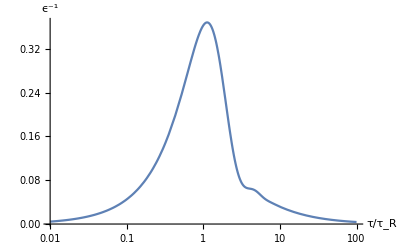

```mathematica
γ=1;
ω0=1;
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^-1"}]
Clear[γ,ω0]
```

```mathematica
γ=1;
ω0=1;

data=List[];

Do[

aux=Table[{τ,ϵ1[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi3.dat",data];

Clear[τR,γ,ω0]
```